```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
(*LS-Periodogram*)
LS[tx_, nP_] := (*Press (2007).Numerical Recipes (3rd ed.).Cambridge University Press.ISBN 0-521-88068-8.*)
 LS[tx, nP] = (*here nP not power, data points in amplitude, i.e. the time series y-values, nP=#of these data points*)
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]/∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]]/(2. ω);(*This tau is really the phase, not oscillation time*)
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
T[periodogram_,rankmax_]:=T[periodogram,rankmax]=Block[{power,ωmax,period},power=Table[periodogram[[i,2]],{i,1,Length[periodogram]}];
ωmax=periodogram[[Position[power,RankedMax[power,rankmax]][[1,1]],1]];
{period=2 π/ωmax,RankedMax[power,rankmax]}];
p[z_,n_]:=p[z,n]=1-(1-Exp[-z])^n;
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

# Periodogram: From Michal’s thesis. For sidereal modulation analysis, we can extract 24h frequency - amplitude constraint from periodogram.

```mathematica
rundat={};
starttime=0;
pta10=pta20=fta10=fta20=erra10=erra20=fta102=fta202={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
ptarun=Table[{},{k,1,dimdesc}];ptarun2=Table[{},{k,1,dimdesc}];
ftarun=Table[{},{k,1,dimdesc}];ftarun2=Table[{},{k,1,dimdesc}];
errarun=Table[{},{k,1,dimdesc}];errarun2=Table[{},{k,1,dimdesc}];
tsadd=2*PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>10)(*accepting only runs with >10cy*)
,
(*Print[descdat[[i]][[4]]];*)
rundat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimrundat=Dimensions[rundat][[1]];
If[i==1,starttime=rundat[[1]][[1]]];
(*For-A*tf/ts*)
ptarun[[i]]=Table[
{
N[(rundat[[;;,1]][[k]]-starttime)/(86164.09054)](*Sidereal Day = 86164s*),
{
((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]](*time*),rundat[[;;,{2,3}]][[k]][[2]]])*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],descdat[[i]][[8]]]+tsadd)))(*a_b <tf>/ts*)
}
},
{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}
];
ftarun[[i]]=Transpose[{ptarun[[i]][[;;,1]],ptarun[[i]][[;;,2]][[;;,1]]}];
errarun[[i]]=Abs[ptarun[[i]][[;;,2]][[;;,2]]];
(*For-A*)
ptarun2[[i]]=Table[{N[(rundat[[;;,1]][[k]]-starttime)/(86164.09054)],{rundat[[;;,{2,3}]][[k]][[1]],Abs[rundat[[;;,{2,3}]][[k]][[2]]]}},{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}];
ftarun2[[i]]=Transpose[{ptarun2[[i]][[;;,1]],ptarun2[[i]][[;;,2]][[;;,1]]}];
errarun2[[i]]=Abs[ptarun2[[i]][[;;,2]][[;;,2]]];
(**)
If[descdat[[i]][[6]]==10,(*Collecting all 10muT cycles*)
{
bpt10=Join[bpt10,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{8,9}]]}]];(*bft is used to plot, bpt is used to calculate mean, width, error on mean*)
bft10=Join[bft10,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];(*error on a_b <tf>/ts*)
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta10=Join[pta10,ptarun[[i]]];(*Combining all runs*)
fta10=Join[fta10,ftarun[[i]]];
erra10=Join[erra10,errarun[[i]]];
},(*Collecting all 20muT cycles*)
{
bpt20=Join[bpt20,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{8,9}]]}]];(*bft is used to plot, bpt is used to calculate mean, width, error on mean*)
bft20=Join[bft20,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];(*error on a_b <tf>/ts*)
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta20=Join[pta20,ptarun[[i]]];(*Combining all runs*)
fta20=Join[fta20,ftarun[[i]]];
erra20=Join[erra20,errarun[[i]]];
}
];
bpt0=Join[bpt0,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,{6,7}]]}]];(*Collecting all 0muT cycles: these are not used, but if need be*)
bft0=Join[bft0,Transpose[{N[(rundat[[;;,1]]-starttime)/(86164.09054)],rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];(*error on a_b <tf>/ts: these are not used, but if need be*)
];
];
(**)
```

## MC+LS

```mathematica
Parallelize[
For[j=1,j≤mcruns,j++,
ftamc={};
For[i=1,i≤Dimensions[totdat][[1]],i++,
RandomSeed[CurrentDate[]];
ftamc=AppendTo[ftamc,{totdat[[i]][[1]],RandomVariate[NormalDistribution[totdat[[i]][[2]][[1]],totdat[[i]][[2]][[2]]]]}];(*picking data points at the same time stamp as real data, with a Normal distribution definited by actual data's central value and error bars*)
];
gramftamc[[j]]=LS[ftamc,np];(*Periodogram of MC*)
];
gramfta=LS[totdatft,np];(*Periodogram of data*)
gramftamcm=Mean[gramftamc];(*Mean of MC*)
gramftamcs=StandardDeviation[gramftamc];(*sigma of MC periodogram*)
]//AbsoluteTiming /(360)(*in h/10*)
```

{2509.78,Null}

```mathematica
(*Phew that took 10d, Dump data set*)
```

## Plotting

```mathematica
lineStyle={Thick,Black};
ln1=Line[{{ 2Pi,0},{2 Pi,3}}];
ln2=Line[{{ 2Pi,0},{4 Pi,3}}];
(*Calculating phase by diving the sine and cosine amplitudes*)
ptgramftap=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramfta[[;;,2]]/gramfta2[[;;,2]]]]}];(*for data*)
ptgramftamcmp=Transpose[{gramftamcm2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]/gramftamcm2[[;;,2]]]]}];(*for MC*)
val2pi=Nearest[ptgramfta[[;;,1]],2Pi][[1]];(*For 24h, locating the frequency*)
Print["Amplitude @ 2π: ", amp2pi=ptgramfta[[Position[ptgramfta,val2pi][[1]][[1]]]][[2]]];(*Extracting the amplitude*)
val2Pi=Nearest[ptgramfta[[;;,1]],4Pi][[1]];(*For 12h, locating the frequency*)
Print["Amplitude @ 4π: ", amp4Pi=ptgramfta[[Position[ptgramfta,val4Pi][[1]][[1]]]][[2]]];(*Extracting the amplitude*)
(*Plotting the power spectra and p-value*)
Export[StringJoin[PicDir,seperator,"Sidereal_pow-1.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{6.11,6.44},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_pow-2.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{2*{6.11,6.44},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_pow_all.png"],ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.002],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","A_B(<SubscriptBox[t, f]>)/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{0.001,49.999},{0,Automatic}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_phase_1.png"],ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{{6.11,6.44},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
Export[StringJoin[PicDir,seperator,"Sidereal_phase_2.png"],ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC+1σ","MC+95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{2*{6.11,6.44},Automatic},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1,ln2}]]
```

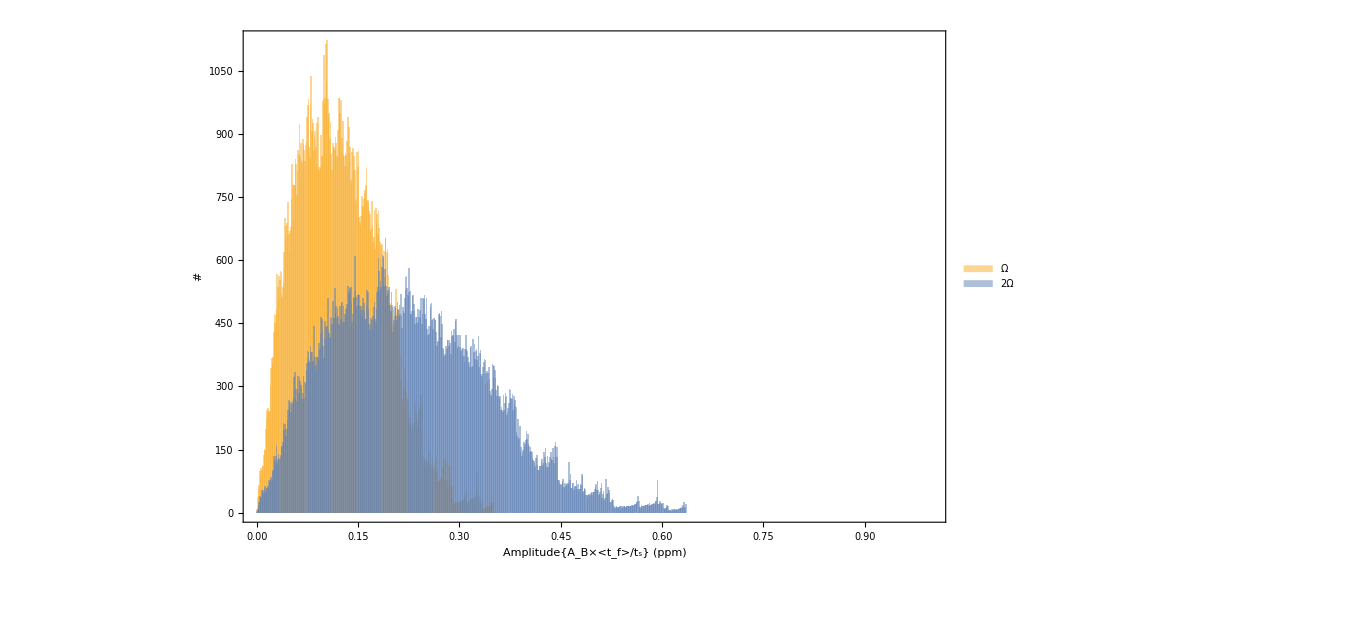
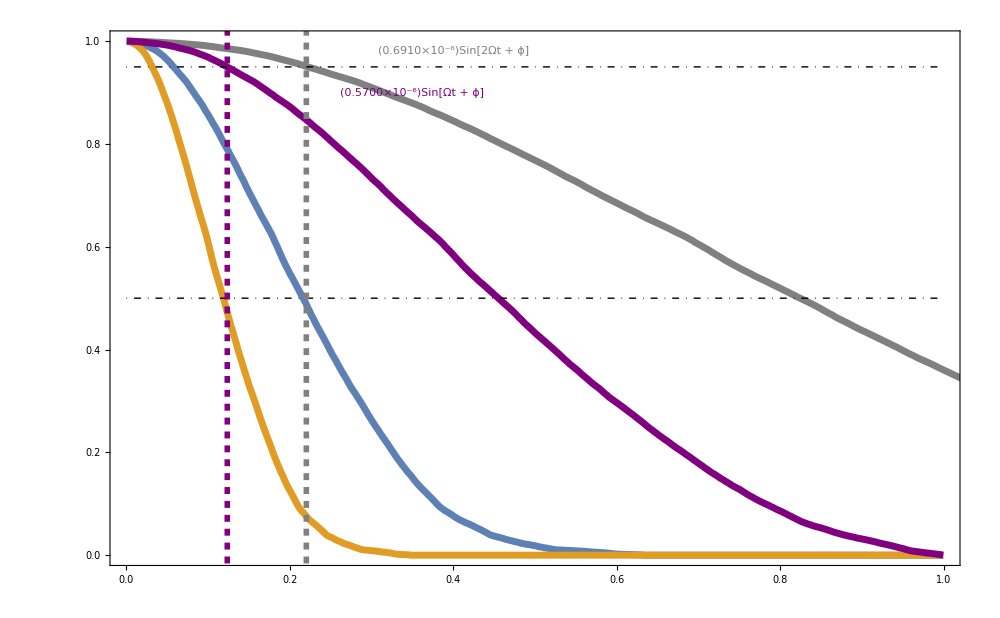

```mathematica
(***)
lineStyle1={Thick,Dashed,Black};
lineStyle2={Thickness[.004],Dashed,Purple};
lineStyle3={Thickness[.004],Dashed,Gray};
ln11=Line[{{ amp2pi,-10},{amp2pi,100}}];
ln21=Line[{{amp2Pi,-10},{amp2Pi,100}}];
(*Combining all the above plots and printing it as one, P-value & power spectra*)
Overlay[{
Histogram[{ptgramfta[[;;,2]],ptgramfta[[;;,2]]},{0,1,.001},ChartLegends->{"Ω","2Ω"},ImagePadding->100,Frame->{True,True,False,False},FrameLabel->{"Amplitude{A_B×<t_f>/t_s} (ppm)","#"},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{{Thickness[.004],Red},{Thickness[.004],Red},Automatic,Automatic}],
Show[{
ListLinePlot[{pthistgramfta,pthistgramfta2,pthistgramfta3,pthistgramfta4},PlotRange->{{0,1},Automatic},ImagePadding->100,Frame->{False,False,True,True},PlotStyle->{{Thickness[.005],Automatic},{Thickness[.005],Automatic},{Thickness[.005],Gray},{Thickness[.005],Purple}},FrameLabel->{{"",Rotate["p-value",180 Degree]},{"",""}},ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->{Automatic,Automatic,{Thickness[.004],Blue},{Thickness[.004],Blue}},
Epilog->{
{Directive[lineStyle2],ln11,Text[Style["(",amp2pi,")Sin[Ωt + ϕ]",FontSize->Large],{.35,.90}]},
{Directive[lineStyle3],ln21,Text[Style["(",amp4pi,")Sin[2Ωt + ϕ]",FontSize->Large],{.4,.98}]}
}],
}]
}]
```